# MS-C1650 - Numerical Analysis Week 18: Lecture 5: Piecewise Interpolation

## Harri Hakula, 2021

## Hermite Interpolation (Textbook version)

Let us implement the method in its pure format.

```mathematica
HermiteInterval[{{x0_?NumericQ,f0_?NumericQ,df0_?NumericQ},{x1_?NumericQ,f1_?NumericQ,df1_?NumericQ}}]:=Block[{h,α,C,x},
h=x1-x0;
C=f0;
α=(3/h^2)(df0+df1)+(6/h^3)(f0-f1);
{
Simplify[-(df0/h)Integrate[t-x1,{t,x0,x}]+(df1/h)Integrate[t-x0,{t,x0,x}]+α Integrate[(t-x0)(t-x1),{t,x0,x}]+C],
x0≤x≤x1
}
]
```

```mathematica
HermiteInterpolation[data:{{_?NumericQ,_?NumericQ,_?NumericQ}..}]:=Block[{int},
Piecewise[HermiteInterval/@Partition[data,2,1]]
]
```

## Examples

### Case 1

```mathematica
fun=Function[ξ,3 ξ^4-2 ξ^2+Sin[ξ]+1];
Dfun=Function[ξ,Evaluate[D[fun[ξ],ξ]]];
DDfun=Function[ξ,Evaluate[D[fun[ξ],{ξ,2}]]];
```

```mathematica
xp=Subdivide[-1,1,3]
```

{-1,-1/3,1/3,1}

```mathematica
data=Transpose[{xp,fun[xp],Dfun[xp]}];
```

```mathematica
hpi=HermiteInterpolation[data]
```

Piecewise[{{1/12 (24+(1+x)^2 (8+9 Cos[1/3])-3 (-1+2 x+3 x^2) (-8+Cos[1])+3 x (1+x)^2 (-32+9 Cos[1/3]+9 Cos[1]+27 Sin[1/3]-27 Sin[1])-12 Sin[1]), -1≤x≤-1/3}, {1/54 (52-72 x^2-27 x (Cos[1/3]-9 Sin[1/3])+243 x^3 (Cos[1/3]-3 Sin[1/3])), -1/3≤x≤1/3}, {1/108 (88-(5-18 x+9 x^2) (-8+9 Cos[1/3])+9 (1-3 x)^2 (8+Cos[1])+108 Sin[1/3]+(1-3 x)^2 (-4+3 x) (32+9 Cos[1/3]+9 Cos[1]+27 Sin[1/3]-27 Sin[1])), 1/3≤x≤1}, {0, True}}]

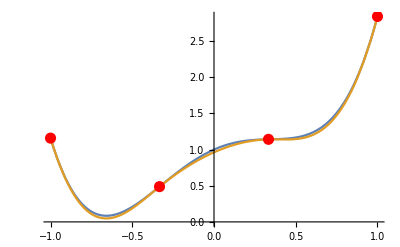

```mathematica
Plot[{fun[x],hpi},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,fun[xp]}]]}]
```

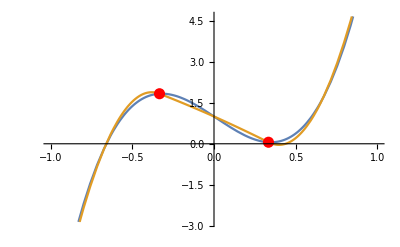

```mathematica
Plot[{Dfun[x],Evaluate[D[hpi,x]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,Dfun[xp]}]]}]
```

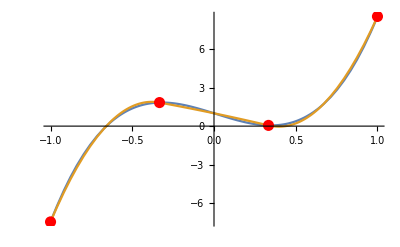

```mathematica
Plot[{Dfun[x],Evaluate[D[hpi,x]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,Dfun[xp]}]]},PlotRange->All]
```

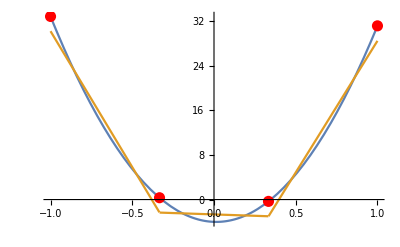

```mathematica
Plot[{DDfun[x],Evaluate[D[hpi,{x,2}]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,DDfun[xp]}]]},PlotRange->All]
```

## Examples

### Case 2

```mathematica
fun=Function[x,Cos[4x]Exp[2x]];
Dfun=Function[x,Evaluate[D[fun[x],x]]];
DDfun=Function[x,Evaluate[D[fun[x],{x,2}]]];
```

```mathematica
xp=Subdivide[-1,1,2]
```

{-1,0,1}

```mathematica
data=Transpose[{xp,fun[xp],Dfun[xp]}];
```

```mathematica
hpi=HermiteInterpolation[data]
```

Piecewise[{{(1+x)^2+(x^2 (5 Cos[4]+4 Sin[4]+4 x (Cos[4]+Sin[4])))/ⅇ^2, -1≤x≤0}, {1+2 x+x^3 (4-4 ⅇ^2 Sin[4])+x^2 (-7+ⅇ^2 (Cos[4]+4 Sin[4])), 0≤x≤1}, {0, True}}]

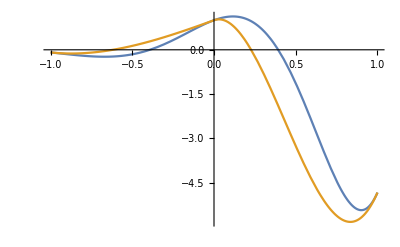

```mathematica
Plot[{fun[x],hpi},{x,-1,1}]
```

```mathematica
xp=Subdivide[-1,1,3]
```

{-1,-1/3,1/3,1}

```mathematica
data=Transpose[{xp,fun[xp],Dfun[xp]}];
```

```mathematica
hpi=HermiteInterpolation[data]
```

Piecewise[{{1/(4 ⅇ^2)(-3 ⅇ^(4/3) (1+x)^2 (3 x (Cos[4/3]-4 Sin[4/3])-2 (Cos[4/3]+2 Sin[4/3]))+(1+3 x)^2 (6 Cos[4]+5 x Cos[4]+4 Sin[4]+4 x Sin[4])), -1≤x≤-1/3}, {1/(12 ⅇ^(2/3))((1-3 x)^2 (8 Cos[4/3]+15 x Cos[4/3]+4 Sin[4/3]+12 x Sin[4/3])-ⅇ^(4/3) (1+3 x)^2 (-4 (Cos[4/3]+Sin[4/3])+3 x (Cos[4/3]+4 Sin[4/3]))), -1/3≤x≤1/3}, {-1/4 ⅇ^(2/3) (-2 (-3 Cos[4/3]+6 Sin[4/3]+ⅇ^(4/3) (Cos[4]+2 Sin[4]))+9 x^3 (-5 Cos[4/3]+4 Sin[4/3]+ⅇ^(4/3) (Cos[4]+4 Sin[4]))-12 x^2 (-8 Cos[4/3]+7 Sin[4/3]+ⅇ^(4/3) (2 Cos[4]+5 Sin[4]))+x (-57 Cos[4/3]+60 Sin[4/3]+ⅇ^(4/3) (13 Cos[4]+28 Sin[4]))), 1/3≤x≤1}, {0, True}}]

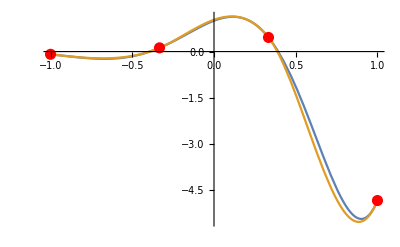

```mathematica
Plot[{fun[x],hpi},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,fun[xp]}]]}]
```

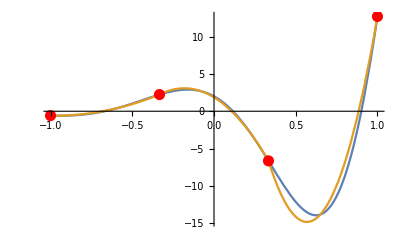

```mathematica
Plot[{Dfun[x],Evaluate[D[hpi,x]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,Dfun[xp]}]]}]
```

```mathematica
Plot[{Dfun[x],Evaluate[D[hpi,x]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,Dfun[xp]}]]},PlotRange->All]
```

-Graphics-

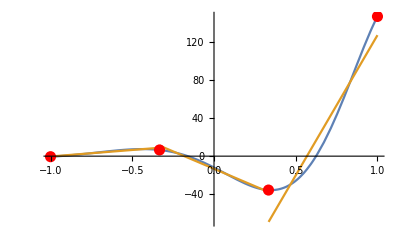

```mathematica
Plot[{DDfun[x],Evaluate[D[hpi,{x,2}]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,DDfun[xp]}]]},PlotRange->All]
```

## Hermite Interpolation (Non-standard)

Let us interpolate the function f(x) = 3 x^4-2 x^2+Sin[x]+1 over the interval x∈[-1,1].

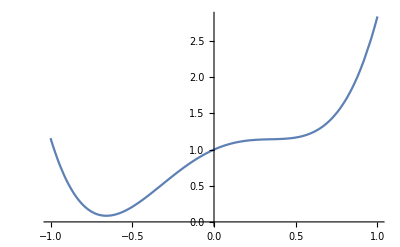

```mathematica
Plot[3 x^4-2 x^2+Sin[x]+1,{x,-1,1}]
```

Choose points and find the values and the derivatives.

```mathematica
fun=Function[x,3 x^4-2 x^2+Sin[x]+1];
Dfun=Function[x,Evaluate[D[fun[x],x]]];
DDfun=Function[x,Evaluate[D[fun[x],{x,2}]]];
```

```mathematica
x=Subdivide[-1,1,6]
```

{-1,-2/3,-1/3,0,1/3,2/3,1}

```mathematica
y=fun/@x
```

{2-Sin[1],19/27-Sin[2/3],22/27-Sin[1/3],1,22/27+Sin[1/3],19/27+Sin[2/3],2+Sin[1]}

```mathematica
dy=Dfun/@x
```

{-8+Cos[1],-8/9+Cos[2/3],8/9+Cos[1/3],1,-8/9+Cos[1/3],8/9+Cos[2/3],8+Cos[1]}

```mathematica
data=MapThread[List[List[#1],#2,#3]&,{x,y,dy}]
```

{{{-1},2-Sin[1],-8+Cos[1]},{{-2/3},19/27-Sin[2/3],-8/9+Cos[2/3]},{{-1/3},22/27-Sin[1/3],8/9+Cos[1/3]},{{0},1,1},{{1/3},22/27+Sin[1/3],-8/9+Cos[1/3]},{{2/3},19/27+Sin[2/3],8/9+Cos[2/3]},{{1},2+Sin[1],8+Cos[1]}}

```mathematica
if=Interpolation[data,Method->"Hermite",InterpolationOrder->1];
```

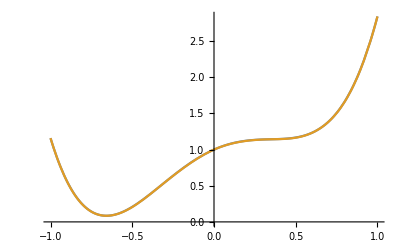

```mathematica
Plot[{fun[x],if[x]},{x,-1,1}]
```

```mathematica
if/@x
N[fun/@x]
Function[ξ,Evaluate[D[if[ξ],ξ]]]/@x
N[Dfun/@x]
```

{2-Sin[1],19/27-Sin[2/3],22/27-Sin[1/3],1,22/27+Sin[1/3],19/27+Sin[2/3],2+Sin[1]}

{1.15853,0.0853339,0.48762,1.,1.14201,1.32207,2.84147}

{-8+Cos[1],-8/9+Cos[2/3],8/9+Cos[1/3],1,-8/9+Cos[1/3],8/9+Cos[2/3],8+Cos[1]}

{-7.4597,-0.103002,1.83385,1.,0.0560681,1.67478,8.5403}

```mathematica
N[Function[ξ,Evaluate[D[if[ξ],{ξ,2}]]]/@x]
N[DDfun/@x]
```

{32.1818,11.9583,-0.335315,-4.66544,-0.995697,10.7103,30.4848}

{32.8415,12.6184,0.327195,-4.,-0.327195,11.3816,31.1585}

## Splines (Natural spline, textbook version)

Let us implement the natural spline in its pure format.

```mathematica
SplineInterval[{
{x0_?NumericQ,f0_?NumericQ,z0_?NumericQ},{x1_?NumericQ,f1_?NumericQ,z1_?NumericQ}
}]:=Block[{x,h,c,d},
h=x1-x0;
c=(1/h)(f1-f0+(h^2/6)(z0-z1));
d=f0-(h^2/6)z0;
{
Expand[(1/6)(1/h)z0(x1-x)^3+(1/6)(1/h)z1(x-x0)^3+c(x-x0)+d],
x0≤x≤x1
}
]
```

```mathematica
SplineInterpolation[data:{{_?NumericQ,_?NumericQ}..}]:=Block[{z,h,f,A,b,dim},
dim=Length[data];
f=data[[All,2]];
z=ConstantArray[0,dim];
h=data[[2,1]]-data[[1,1]];
A=If[dim-2==1,
SparseArray[{Band[{1,1}]->2 h/3},{dim-2,dim-2}],
SparseArray[{Band[{1,1}]->2 h/3,Band[{1,2}]->h/6,Band[{2,1}]->h/6},{dim-2,dim-2}]
];
b=(1/h)(f[[1;;-3]]-2f[[2;;-2]]+f[[3;;-1]]);
z[[2;;-2]]=LinearSolve[A,N@b];
Piecewise[SplineInterval/@Partition[MapThread[Append,{data,z}],2,1]]
]
```

## Slide

### Case 1

```mathematica
fun=Function[x,3 x^4-2 x^2+Sin[x]+1];
Dfun=Function[x,Evaluate[D[fun[x],x]]];
DDfun=Function[x,Evaluate[D[fun[x],{x,2}]]];
```

```mathematica
xp=Subdivide[-1,1,3]
```

{-1,-1/3,1/3,1}

```mathematica
data=Transpose[{xp,fun[xp]}];
```

```mathematica
spi=SplineInterpolation[{{-1,1},{0,2},{1,-1}}]
```

Piecewise[{{2.-1. x-3. x^2-1. x^3, -1≤x≤0}, {2.-1. x-3. x^2+1. x^3, 0≤x≤1}, {0, True}}]

```mathematica
spi=SplineInterpolation[data]
```

Piecewise[{{0.684181+1.44091 x+2.87288 x^2+0.957627 x^3, -1≤x≤-1/3}, {0.637037+1.01661 x+1.6 x^2-0.315254 x^3, -1/3≤x≤1/3}, {0.649153+0.907573 x+1.92712 x^2-0.642373 x^3, 1/3≤x≤1}, {0, True}}]

```mathematica
spi/.{x->-1/3}
```

0.48762

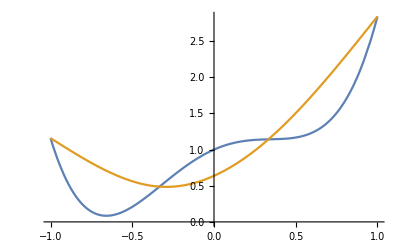

```mathematica
Plot[{fun[x],spi},{x,-1,1}]
```

```mathematica
xp=Subdivide[-1,1,6]
```

{-1,-2/3,-1/3,0,1/3,2/3,1}

```mathematica
data=Transpose[{xp,fun[xp]}];
```

```mathematica
spi=SplineInterpolation[data]
```

Piecewise[{{7.10331+26.5646 x+30.9297 x^2+10.3099 x^3, -1≤x≤-2/3}, {0.578428-2.79737 x-13.1132 x^2-11.7116 x^3, -2/3≤x≤-1/3}, {1.+0.996785 x-1.73077 x^2-0.329116 x^3, -1/3≤x≤0}, {1.+0.996785 x-1.73077 x^2+0.0554997 x^3, 0≤x≤1/3}, {0.589663+4.68981 x-12.8099 x^2+11.1346 x^3, 1/3≤x≤2/3}, {6.69156-22.7687 x+28.378 x^2-9.45932 x^3, 2/3≤x≤1}, {0, True}}]

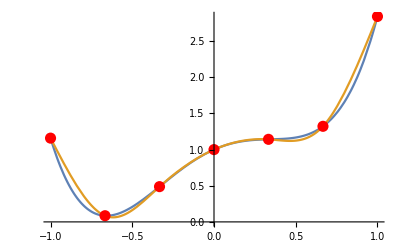

```mathematica
Plot[{fun[x],spi},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,fun[xp]}]]}]
```

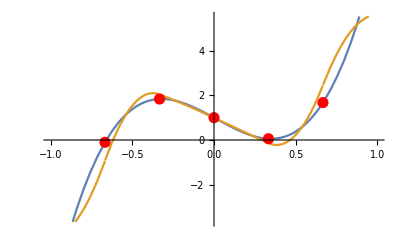

```mathematica
Plot[{Dfun[x],Evaluate[D[spi,x]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,Dfun[xp]}]]}]
```

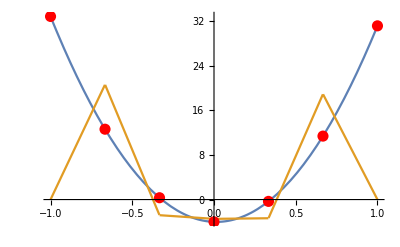

```mathematica
Plot[{DDfun[x],Evaluate[D[spi,{x,2}]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,DDfun[xp]}]]},PlotRange->All]
```

## Slide

### Case 2

```mathematica
fun=Function[x,Cos[4x]Exp[2x]];
Dfun=Function[x,Evaluate[D[fun[x],x]]];
DDfun=Function[x,Evaluate[D[fun[x],{x,2}]]];
```

```mathematica
xp=Subdivide[-1,1,3]
```

{-1,-1/3,1/3,1}

```mathematica
data=Transpose[{xp,fun[xp]}];
```

```mathematica
spi=SplineInterpolation[data]
```

Piecewise[{{0.992652+3.84325 x+4.1432 x^2+1.38107 x^3, -1≤x≤-1/3}, {0.70177+1.2253 x-3.71063 x^2-6.47276 x^3, -1/3≤x≤1/3}, {0.273456+5.08012 x-15.2751 x^2+5.09169 x^3, 1/3≤x≤1}, {0, True}}]

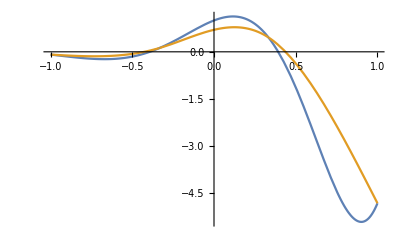

```mathematica
Plot[{fun[x],spi},{x,-1,1}]
```

```mathematica
xp=Subdivide[-1,1,3]
```

{-1,-1/3,1/3,1}

```mathematica
data=Transpose[{xp,fun[xp]}];
```

```mathematica
spi=SplineInterpolation[data]
```

Piecewise[{{0.992652+3.84325 x+4.1432 x^2+1.38107 x^3, -1≤x≤-1/3}, {0.70177+1.2253 x-3.71063 x^2-6.47276 x^3, -1/3≤x≤1/3}, {0.273456+5.08012 x-15.2751 x^2+5.09169 x^3, 1/3≤x≤1}, {0, True}}]

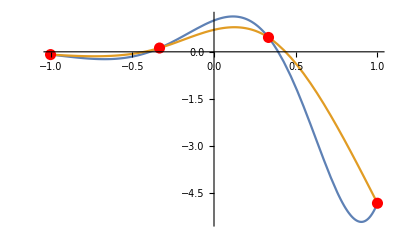

```mathematica
Plot[{fun[x],spi},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,fun[xp]}]]}]
```

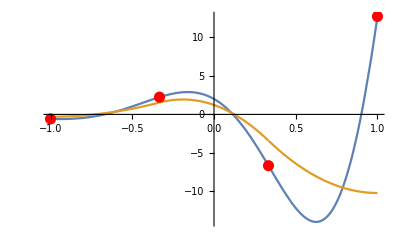

```mathematica
Plot[{Dfun[x],Evaluate[D[spi,x]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,Dfun[xp]}]]}]
```

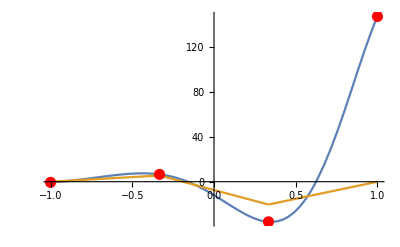

```mathematica
Plot[{DDfun[x],Evaluate[D[spi,{x,2}]]},{x,-1,1},Epilog->{Red,PointSize[0.02],Point[Transpose[{xp,DDfun[xp]}]]},PlotRange->All]
```

## Spline (Non-standard)

```mathematica
is=Interpolation[N@Transpose[{x,y}],Method->"Spline",InterpolationOrder->3];
```

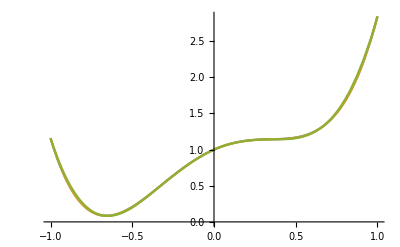

```mathematica
Plot[{fun[x],if[x],is[x]},{x,-1,1}]
```

```mathematica
is/@x
N[fun/@x]
Function[ξ,Evaluate[D[is[ξ],ξ]]]/@x
N[Dfun/@x]
```

{1.15853,0.0853339,0.48762,1.,1.14201,1.32207,2.84147}

{1.15853,0.0853339,0.48762,1.,1.14201,1.32207,2.84147}

{-6.98768,-0.228927,1.86521,1.00009,0.0239383,1.80282,8.05994}

{-7.4597,-0.103002,1.83385,1.,0.0560681,1.67478,8.5403}

```mathematica
Function[ξ,Evaluate[D[is[ξ],{ξ,2}]]]/@x
N[DDfun/@x]
```

{27.2732,13.2793,-0.714521,-4.47619,-1.38072,12.054,25.4887}

{32.8415,12.6184,0.327195,-4.,-0.327195,11.3816,31.1585}